## Study the evolution of H(θ,φ;𝒫) w.r.t change of MOIs

## 𝒫 is the parameter set (V,γ, ℐ_1,ℐ_2,ℐ_3)

### Adds a special color scheme

```mathematica
CoolColor[ z_ ] :=RGBColor[z,1-z,1];
```

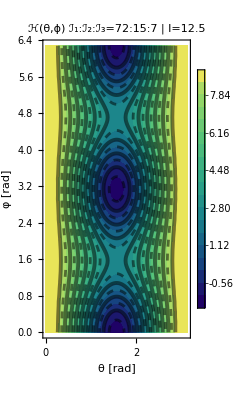

```mathematica
IF[X_]:=1/(2*X);
H[I_,θ_,φ_,A1_,A2_,A3_,V_,γ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ]^2(A1*Cos[φ]^2+A2*Sin[φ]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ]-V*(2j-1)/(j+1)Sin[γ+π/6];
CPH[spin_,I1_,I2_,I3_,V_,γ_]:=ContourPlot[H[spin,θ,φ,IF[I1],IF[I2],IF[I3],V,γ*π/180]/.{j->13/2},{θ,0,π},{φ,0,2π},AspectRatio->Automatic,Contours->18,ContourStyle->{{Black,Dashed,Thickness[0.005]},{Black,Thick,Thickness[0.007]}},ColorFunction->"BlueGreenYellow",ImageSize->Scaled[0.5],Frame->True,Axes->False,FrameStyle->Directive[Thick,Black],FrameLabel->{"θ [rad]","φ [rad]"},PlotLabel->Text[Style[StringTemplate["                  ℋ(θ,ϕ)\nℐ_1:ℐ_2:ℐ_3=``:``:`` | I=``"][I1,I2,I3,spin],Black,FontFamily->"Times New Roman",18]],PlotLegends->Automatic,LabelStyle->{Black,17,FontFamily->"Times New Roman"}];
Show[CPH[12.5,72,15,7,2.1,22]]
```

```mathematica
(*Manipulate[CPH[12.5,I1,I2,I3,2.1,22],{I1,20,80},{I2,1,50},{I3,1,50}]*)
```

## Make a graphics grid with the four spin values

### Parameters were obtained from the double-energy-shift fitting procedure

```mathematica
grid[I1_,I2_,I3_,I4_]:=GraphicsGrid[{{Show[CPH[I1,72,15,7,2.1,22]],Show[CPH[I2,72,15,7,2.1,22]]},{Show[CPH[I3,72,15,7,2.1,22]],Show[CPH[I4,72,15,7,2.1,22]]}},ImageSize->Scaled[2.5],Frame->All];
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/Contour-Grid_doubleShift.png",Show[grid[12.5,15.5,18.5,25.5]]];
```

## Separate contour plots for each spin value

## spin - 1

```mathematica
Show[CPH[12.5,72,15,7,2.1,22]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/Contour-Spin1_DS.png",Show[CPH[12.5,72,15,7,2.1,22]]];
```

-Graphics-

## spin - 2

```mathematica
Show[CPH[15.5,72,15,7,2.1,22]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/Contour-Spin2_DS.png",Show[CPH[15.5,72,15,7,2.1,22]]];
```

-Graphics-

```mathematica
Show[CPH[18.5,72,15,7,2.1,22]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/Contour-Spin3_DS.png",Show[CPH[18.5,72,15,7,2.1,22]]];
```

-Graphics-

```mathematica
Show[CPH[25.5,72,15,7,2.1,22]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/Contour-Spin4_DS.png",Show[CPH[25.5,72,15,7,2.1,22]]];
```

-Graphics-

```mathematica
(*Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Data/Energy_Function/CP_animation_I2change.gif",Table[CPH[12.5,73,moi,3,8.1,19],{moi,3,73,0.5}]];*)
```

```mathematica
(*Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Data/Energy_Function/CP_animation_I3change.gif",Table[CPH[12.5,73,3,moi,8.1,19],{moi,3,73,0.5}]];*)
```